# Home work 1

-1

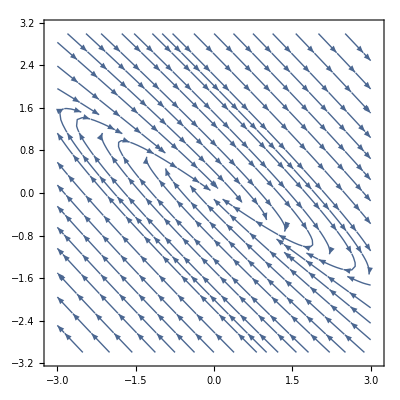

```mathematica
sigma=-1
StreamPlot[{(3+sigma)x+4y,-9/4x+(sigma-3)y},{x,-3,3},{y,-3,3}]
```

```mathematica
A={{1,3},{-2,-1}};
X[t_]:={x[t],y[t]};
system=X'[t]==A.x[t];
Plot[system,{t,-5,5}]
sol = DSolve[system,{x,y},t]
```

-Graphics-

DSolve::dsvar: -1.11851 cannot be used as a variable.

DSolve[{0,0}=={{1,3},{-2,-1}}.(-1.87083)[-1.11851],{-1.87083,9.9519×10^-6},-1.11851]

```mathematica
x=4*Sqrt[5]*Sin[Sqrt[5]*t]/5+Cos[Sqrt[5]*t];
y=-3*Sqrt[5]*Sin[Sqrt[5]*t]/5+Cos[Sqrt[5]*t];
angle=x/y;

f[t_]=Norm[{x[t],y[t]}]
f[-1.11851]
FunctionPeriod[angle,t]
ParametricPlot[{x,y},{t,-2,2}]
```

Set::write: Tag Real in 1.87083[t_] is Protected.

√(Abs[(-1.87083)[-1.11851]]^2+Abs[9.9519×10^-6[-1.11851]]^2)

1.87083[-1.11851]

FunctionPeriod[-187988.,-1.11851]

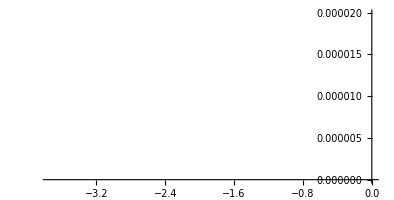
```mathematica
-Graphics-

system={theta'[t]==omega[t],
		omega'[t]==-g/l*sin[theta[t]]-gamma/m*omega[t]};

system2={y[t]==t0/theta0*omega0*y[t],
-g*t0/omega0/l*Sin[theta0*x[t]]-gamma/m*t0*y[t]==-Sin[x[t]]-sigma*y[t]}
NDsolve[system2,{omega0,t0,theta0,sigma}]
```

-Graphics-

{y[t]==(omega0 t0 y[t])/theta0,-(g t0 Sin[theta0 x[t]])/(l omega0)-(gamma t0 y[t])/m==-Sin[x[t]]-sigma y[t]}

NDsolve[{y[t]==(omega0 t0 y[t])/theta0,-(g t0 Sin[theta0 x[t]])/(l omega0)-(gamma t0 y[t])/m==-Sin[x[t]]-sigma y[t]},{omega0,t0,theta0,sigma}]

```mathematica
{y[t]==(omega0 t0 y[t])/theta0,-(g Sin[theta0 x[t]] t0)/(l omega0)-(gamma t0 y[t])/m==-Sin[x[t]]-sigma y[t]}
```

```mathematica
Dsolve[{y[t]==(omega0 t0 y[t])/theta0,-(g Sin[theta0 x[t]] t0)/(l omega0)-(gamma t0 y[t])/m==-Sin[x[t]]-sigma y[t]},{omega0},{t,gamma,l,g,m,y,x}]
```